```mathematica
ω:=2
ω2:=0.5
Ω:=5
ϕ:=π/2
ϕ2:=0
Φ:=0
λ:=0.75
```

```mathematica
f[x_]:= Exp[Ω*Sin[ω*x+ϕ]+Φ]/(Exp[Ω])
g[x_]:=Exp[-λ*Mod[x,2*π]]*Sin[ω*Mod[x,2*π]+ϕ]
```

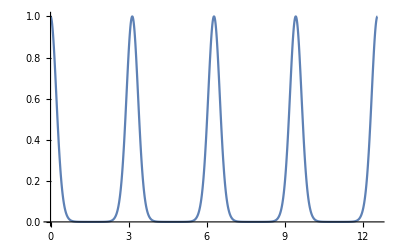

```mathematica
Plot[f[x],{x,0,4*π}]
```

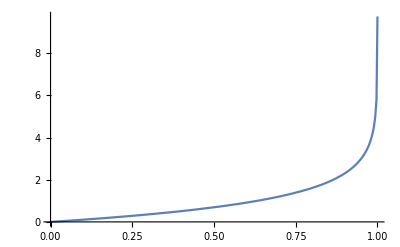

```mathematica
Plot[Log[1/(1-x)],{x, 0, 4*π},PlotRange->All]
```